# Graphics and Visualization

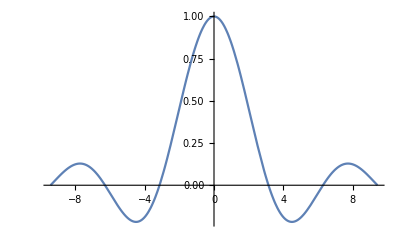

```mathematica
Plot[Sinc[x],{x,-3Pi,3Pi}]
```

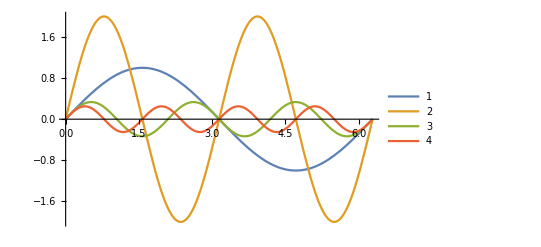

```mathematica
Plot[{Sin[x],2Sin[2x],1/3Sin[3x],1/4Sin[4x]},{x,0,2Pi},PlotLegends->Automatic]
```

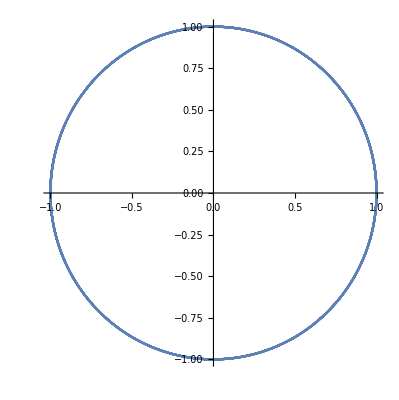

```mathematica
ParametricPlot[{Cos[5t],Sin[5t]},{t,0,2Pi}]
```

```mathematica
Plot3D[Sin[x-Sin[y]],{x,0,3Pi},{y,0,4Pi}]
```

-Graphics3D-

```mathematica
Plot3D[{Sin[x-Sin[y]],Sin[y-Cos[x]]},{x,0,3Pi},{y,0,4Pi},
PlotStyle->{Red,Cyan}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{t/5,Sin[t],2Cos[t]},{t,0,6Pi}]
```

-Graphics3D-

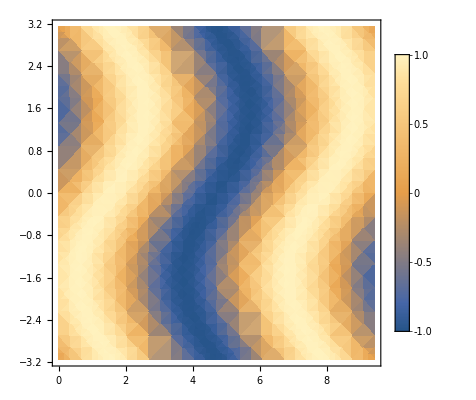
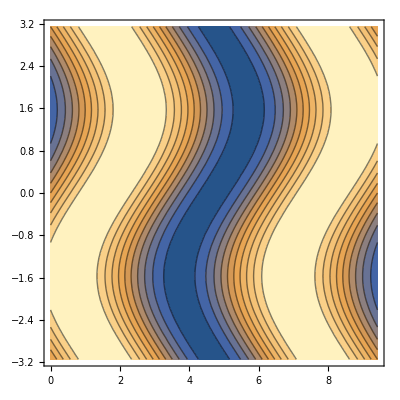
{-Graphics-,-Graphics3D-,-Graphics-}

```mathematica
{DensityPlot[Sin[x-Sin[y]],{x,0,3Pi},{y,-Pi,Pi},PlotLegends->Automatic],Plot3D[Sin[x-Sin[y]],{x,0,3Pi},{y,-Pi,Pi}],
ContourPlot[Sin[x-Sin[y]],{x,0,3Pi},{y,-Pi,Pi},
Contours->10]}
```

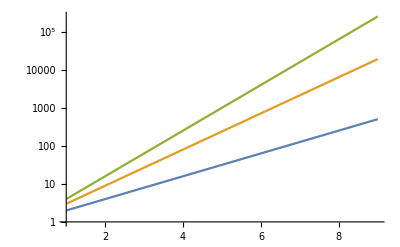

```mathematica
LogPlot[{2^x,3^x,4^x},{x,1,9}]
```

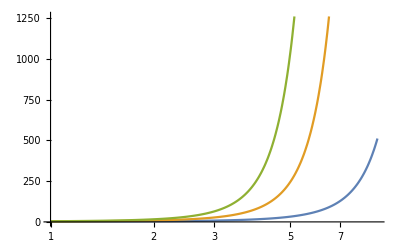

```mathematica
LogLinearPlot[{2^x,3^x,4^x},{x,1,9}]
```

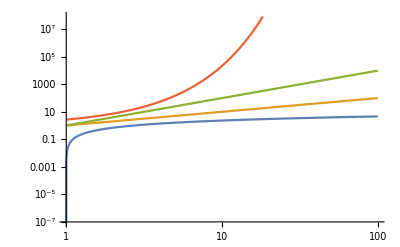

```mathematica
LogLogPlot[Tooltip[{Log[x],x,x^2,E^x}],{x,1,100}]
```

```mathematica
LogLogPlot[{Log[x],x,x^2,E^x},{x,1,100}]
```

-Graphics-

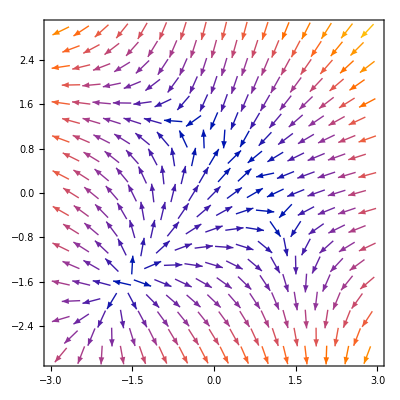

```mathematica
VectorPlot[{1-x^2-y,1-x-y^2},{x,-3,3},{y,-3,3}]
```

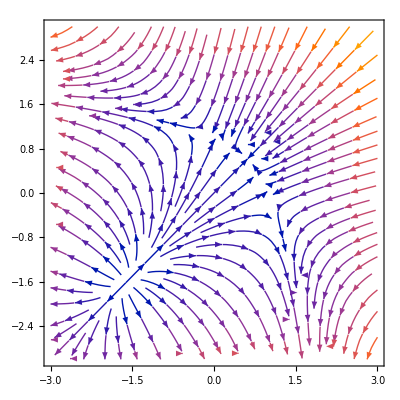

```mathematica
StreamPlot[{1-x^2-y,1-x-y^2},{x,-3,3},{y,-3,3}]
```

```mathematica
Manipulate[PolarPlot[Sin[n x],{x,0,Pi}],{n,1,20}]
```

```mathematica
mat=RandomInteger[{0,1},{50,50}];
ArrayPlot[mat]
```

-Graphics-

```mathematica
champData=WeatherData["KCMI","MeanTemperature",{{2019,1},{2019,12},"Day"}];
```

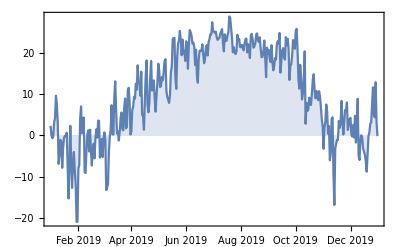

```mathematica
DateListPlot[champData,Joined->True,Filling->Axis]
```

WolframAlphaQueryParseResults

TimeSeries[…]

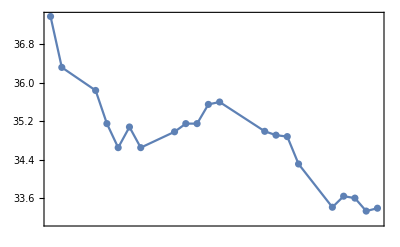

```mathematica
DateListPlot[%,Joined->True,Mesh->All]
```

```mathematica
InteractiveTradingChart["NYSE:FDX",{DatePlus[-1000],DatePlus[0]}]
```

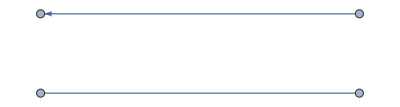

```mathematica
Graph[{2<->3,4->6}]
```

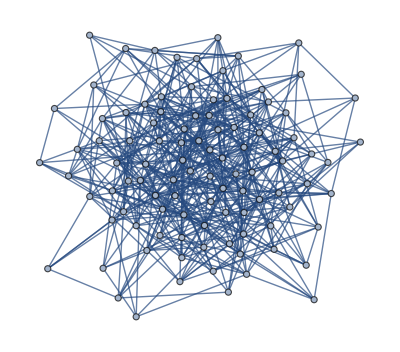

```mathematica
RandomGraph[{100,500}]
```

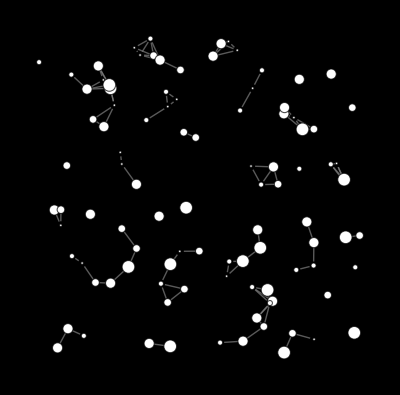

```mathematica
RandomGraph[SpatialGraphDistribution[100,0.08],
VertexStyle->White,
EdgeStyle->Gray,
Background->Black,
VertexSize->Table[i->RandomInteger[{1,5}],{i,100}]]
```

```mathematica
Options[Plot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelingSize→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLayout→Automatic,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

```mathematica
Manipulate[Graphics3D[RandomPolyhedron[n]],{n,3,20,1}]
```

```mathematica
Manipulate[Graphics3D[RandomPolyhedron[n]],{n,3,20,1},AutoAction->True,Deployed->True]
```